### Define some test functions

```mathematica
f1[z_]:=(z^2-I)/(2 z^2+2 I )
```

```mathematica
f2[z_]:=(z^2-I)/(2 z^2+2 I )-1/2
```

### Define a function to generate a color from a point in the complex plane

This function colors the complex plane by argument, blending to white below a distance from the origin rinner and fading to black at a distance router.

```mathematica
colorMap[z_,rinner_,router_]:= Hue[Arg[z]/(2Pi),If[Abs[z]<rinner,Sin[Abs[z]/rinner  Pi/2]^2,1],1-(Abs[z]/router)^2]
```

### Construct a function to visualize the functions

The following input is required:
f — a complex function to visualize
color — a function that maps the complex plane to a color
{xmin,xmax}, {ymin,ymax} — region of the complex plane to visualize.
rinner, router — additional input to the colormap as defined above

Very occasionally, one might have to adjust the value in PlotPoints to a higher value if the visualization is insufficiently smooth

```mathematica
visualizeMap[f_,color_,{xmin_,xmax_},{ymin_,ymax_},{rinner_,router_}]:=ParametricPlot[{x,y},{x,xmin,xmax},{y,xmin,xmax},ColorFunction-> Function[{x,y},color[f[x+I y],rinner,router]],ColorFunctionScaling-> False,Mesh-> False,PlotPoints-> 100,Axes-> False]
```

### Visualize the test functions

The Identity map allows one to investigate the effect of Rinner and Router:

```mathematica
Manipulate[visualizeMap[Identity,colorMap,{-2,2},{-2,2},{rinner,router}],{{rinner,0.2},0.0001,1},{{router,1},0.0001,2},SaveDefinitions-> True]
```

And now for the example plots—one can adjust the radii to suit.

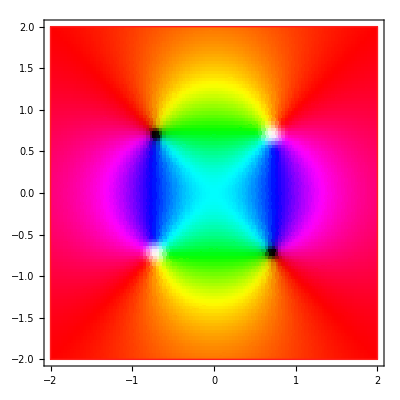

```mathematica
visualizeMap[f1,colorMap,{-2,2},{-2,2},{0.1,10}]
```

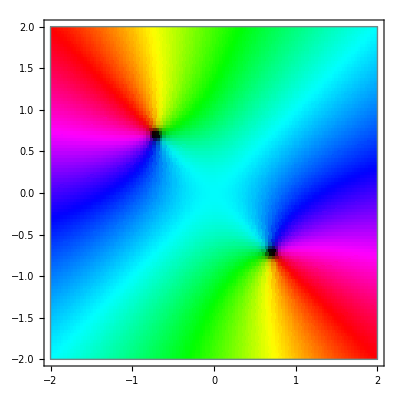

```mathematica
visualizeMap[f2,colorMap,{-2,2},{-2,2},{0.1,10}]
```

Visualizations of well - known functions

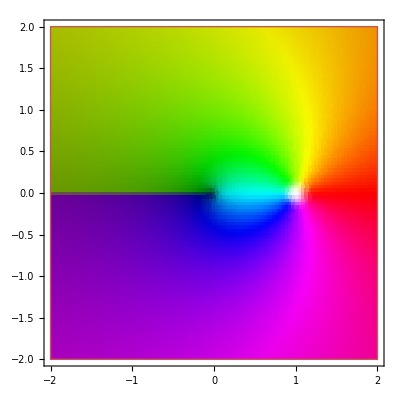

```mathematica
visualizeMap[Log,colorMap,{-2,2},{-2,2},{0.2,5}]
```

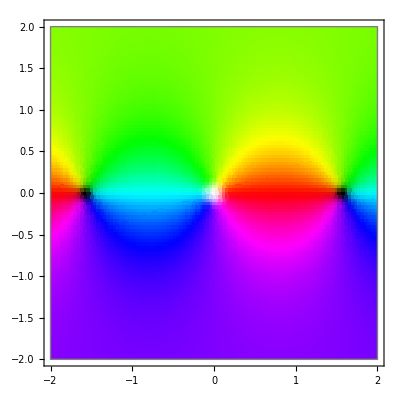

```mathematica
visualizeMap[Tan,colorMap,{-2,2},{-2,2},{0.2,20}]
```

The obligatory Riemann Zeta function :)

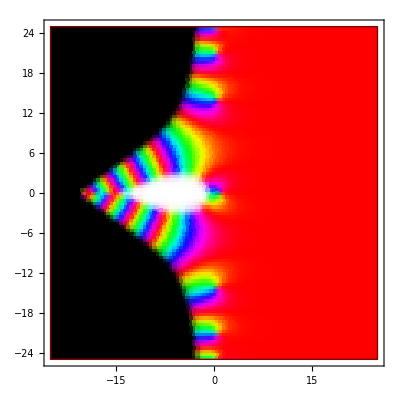

```mathematica
visualizeMap[Zeta,colorMap,{-25,25},{-25,25},{0.2,100}]
```